# Vaje za 3. teden

2. 3. in 3. 3. 2022

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100. Celico začnite z znakom =.

```mathematica
(* = *)
```

WolframAlphaQueryResults

## Naloga 1

Določi 443. števko v decimalnem zapisu števila pi.

```mathematica
(* i hate english:) *)
```

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

```mathematica
(* Če ne dela tuki poglej na WolframAlpha *)
```

WolframAlphaQueryParseResults

[{f[x]==1+2 x+3 x^2,g[x]==4-4 x^4},x]

```mathematica
(* Nevemo točno zakaj ne dela, vrjetno ji ni všeč da funkcije niso impicitno podane *)
```

Izračunaj f(3), kjer je f(x)=1+1/x.

WolframAlphaQueryResults

Jana and Matej have 1536 apples.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 2

Določi površino Slovenije in skupno dolžno njene meje.

```mathematica
(* oranžni okvirčki so entitete *)
```

WolframAlphaQueryParseResults

20273. km^2

WolframAlphaQueryResults

1133. km

Koliko Slovenij prekrije površino Antarktike?

```mathematica
(* ni lih odgovor ki smo ga želeli, ker ne razume kaj želimo, vendar nam vseeno nekaj da *)
```

WolframAlphaQueryResults

Slovenia | 20273 km^2  (square kilometers)  (world rank: 157^th)
Antarctica | 1.321×10^7 km^2  (square kilometers)

```mathematica
(*Najprej Antarctica da jo da v števec*)
```

WolframAlphaQueryParseResults

{651.606}

Kolikšna je temperatura sonca?

WolframAlphaQueryParseResults

5772. K

## Naloga 3

V tej nalogi si bomo pripravili nabor podatkov in s pomočjo tega nabora naredili primer preproste statistične analize.

### Priprava podatkov

Definiraj seznam vseh držav EU. Pomagaš si lahko z naravnim jezikom.

drzave=WolframAlphaQueryParseResults

{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Ireland,Italy,Latvia,Lithuania,Luxembourg,Malta,Netherlands,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden}

Kolikšna je dolžina seznama (tj. število držav Evropske unije)?

WolframAlphaQueryResults

27

```mathematica
Length[drzave]
```

27

Poišči število vseh lastnosti, ki jih imajo države s tega seznama. Nasvet: ukaz EntityProperties. V pomoč vam bo tudi dokumentacija EntityProperty.

```mathematica
EntityProperties[First[drzave]]
```

{adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population,obese adults,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,aggregate weekly hours index,agricultural irrigated land fraction,agricultural land fraction,agricultural production index,agricultural production per capita index,agricultural products,consumption,consumption per capita,harvest area,harvest area per capita,production,production per capita,average yield,yield per capita,arrivals by air,aircraft carriers,air force,airports,air transport,alcohol fuel,total primary energy,alternate names,AM radio stations,annual annulments,annual births,annual deaths,annual divorces,annual HIV/AIDS deaths,annual marriages,antenatal care coverage,annual-crop land area,annual-crop land fraction,total area,armored infantry fighting vehicles,armored personnel carriers,army,artillery,attack helicopters,automobile production,average hourly earnings,average length of stay,average number of meetings with tax officials,average time to clear exports through customs,average weekly hours,average weekly overtime hours,aviation gasoline,bankers acceptance rate,bank prime loan rate,bank prime loan rate changes,benefits cost index,birth rate fraction,births attended by skilled health personnel,births by caesarean section,book titles published,bordering countries/regions,shared border lengths,full boundary length,burden of customs procedure,number of burglaries,rate of burglary,business activity index,professional arrivals,business entry rate,business extent of disclosure,calling code,capacity utilization rate,capital city,capital location,S&P/Case-Shiller home price index,central bank intervention,certificate of deposit,changes in inventories,checkable deposits,chemicals fraction of manufacturing value added,child employment,child population,vitamin A supplementation,children not enrolled in schools,overweight children,antimalarial treatment for fever,stunted children,underweight children,children with ARI symptoms taken to facility,diarrheal treatment with ORT,children sleeping under insecticide-treated nets,cinema attendance,number of cinemas,cinema seats,civilian employment population ratio,civilian labor force,civilian participation rate,civilian unemployment rate,classes,climate types,lignite brown coal,coal,coal,coast guard,coastline length,commercial banks assets,commercial banks credit,commercial paper,commercial paper of nonfinancial companies,community and traditional health workers,community and traditional health workers per capita,compensation per hour index,school completion rate,prevalence of condom use by young people,construction value added,consumer credit,consumer price index,consumer sentiment,container port traffic,continent,contraceptive prevalence,contributing family workers,contributing family workers fraction,conventional mortgage rate,corporate bond yield,corporate capital consumption adjustment,corporate cash flow,corporate dividends,corporate inventory valuation adjustment,corporate profits,corporate proprietors income,typical cost of business start up procedures,typical cost to export one container,typical cost to import one container,country code,consumer price index,CPIA rating,credit depth of information,total rate of crime,total number of crimes,perennial-crop land area,perennial-crop land fraction,currency code,currency in circulation,currency name,currency short name,currency unit,current account,current account balance,current expenditure on health,average daily hotel stays,daily newspaper circulation,death rate fraction,debt measure,DEC alternative conversion factor,demand deposits,dentistry personnel,dentistry personnel per capita,dependencies,dependency parent,deposit interest rate,deposits with Federal Reserve banks,destroyers,discount rate changes,discount window borrowing,discrepancy in expenditure estimate of GDP,disposable personal income,typical documents required per export shipment,typical documents required per import shipment,improved drinking water sources,natural gas,natural gas,ease of doing business,economic aid,economically active children,total school duration,effective federal funds rate,elderly population,electrical grid frequency,electrical grid plug images,electrical grid plug codes,electrical grid socket images,electrical grid socket codes,electrical grid voltages,electricity from biomass,electricity from fossil fuels,geothermal electricity,hydroelectric electricity,pumped-storage hydroelectricity,nuclear electricity,electricity from solar, tide, or waves,total electricity,electricity from renewables,electricity from wind,falling water resources for electric power,emigration rate of tertiary educated,employees compensation,self-employed with employees,employers fraction,employment,employment cost index,employment fraction,employment to population ratio,school ending age,entity classes,environmental agreements,environmental issues,ethnic groups,ethnic mix,exchange rate,expenditure fractions,expenditure on ancillary services,expenditure on day care,health spending,expenditure on home health care,expenditure on in-patient care,expenditure on medical services,expenditure on out-patient care,expenditure on over-the-counter medicines,expenditure on prescription medicines,expenditure per student,expenditure per student fraction of GDP per capita,export commodities,export partners,export partners fractions,exports as a capacity to import,export value,extended credit borrowings,external balance,external debt,factors affecting reserve balances of depository institutions,federal debt,federal deficit,federal demand deposits,federal demand deposits and note balances,federal investment,federal note balances,Federal Reserve bank discount rate,federal surplus,female adult population,female child population,female elderly population,female infant mortality fraction,female life expectancy,female median age,female population,fertilizer consumption,fertilizer production,FHA mortgage rate,fighters,ground-attack fighters,final consumption expenditure,final sales of domestic product,final sales to domestic purchasers,firms formally registered when operations started,firms offering formal training,firms using banks to finance investment,firms with female participation in ownership,fiscal year date,fish production,fixed broadband internet subscribers,fixed capital consumption,flag,flag description,flag image,flexible seasonal credit rate,FM radio stations,food, beverages and tobacco fraction of manufacturing value added,food production index,food production per capita index,number of rapes,rate of rape,foreign exchange reserves,change in foreign owned assets,foreign owned ships,foreign registered ships,forest and woodland area,freshwater withdrawals,freshwater withdrawals fraction,frigates,full coordinates,full name,full native names,gas-diesel oils,GDP,GDP deflator,GDP per employed person,general government final consumption expenditure,Gini index,gross national income,government consumption expenditures and gross investment,government current expenditures,government current receipts,government debt,government education spending as portion of GNI,government investment,government receipts,government saving,government surplus,grants in aid,greenhouse gas emissions,gross capital formation,gross domestic income,GDP,Gross Domestic Purchases,gross domestic savings,gross fixed capital formation,gross national expenditure,gross national expenditure deflator,GNP,gross savings,GSP,gross value added at factor cost,groups,total guests in hotels and similar accommodations,has polygon?,Human Development Index,highest elevation,highest point,HIV-AIDS death rate fraction,HIV/AIDS fraction,HIV/AIDS population,home ownership rate,hospital beds,hours worked index,household credit market outstanding debt,household debt service,household final consumption expenditure,household financial obligation,FHFA home price index,FHFA home price index annual average,new single-family home sales,housing affordability index,housing permits,housing starts,households,illiteracy rate,implicit price deflator,import commodities,import partners,import partners fractions,import value,improved sanitation,income payments,income receipts,income share,independence date,independence year,industrial production,industrial production growth,infant mortality fraction,infectious diseases,inflation rate,inflation expectation,inflation rate,informal payments to public officials,institutional money funds,intake rate in grade 1,interest rate spread,international migrant stock,international organizations,international organizations observer,internet code,internet hosts,average broadband download rate,average broadband upload rate,internet usage,inventory to sales ratio,investment on medical facilities,IP addresses,total IRA and Keogh accounts,irrigated land area,irrigated land fraction,Islamic Revolutionary Guard corps,firms with ISO quality certification,ISO name,International Telecommunication Union region,laboratory health workers,laboratory health workers per capita,labor force,labor force fraction,labor participation rate,land area,crop land area,languages,language dialects,language fractions,number of larcenies,rate of larceny,largest cities,latitude,lead time to export,lead time to import,annual abortions,leisure arrivals,lending interest rate,license plate code,life expectancy,liner shipping connectivity index,liquid assets,literacy rate,livestock population,logistics performance index,longitude,long-term unemployment rate,losses due to theft, robbery, vandalism, and arson,lowest elevation,lowest point,M2 interest rate,M2 minus interest rate,machinery and transport equipment fraction of manufacturing value added,main battle tanks,major industries,major ports,male adult population,male child population,male elderly population,male infant mortality fraction,male life expectancy,male median age,male population,management time dealing with officials,manufacturers new orders,marine corps,protected fraction of territorial waters,maritime claims,meat production,median age,median home sale price,median home value,median household income,memberships,merchant ships,merchant ships dead weight,merchant ships gross,merchant ship types,military age females,military age males,military age population,military age rate,military expenditure fraction,military expenditures,military fit females,military fit males,military fit population,minimum wage,miscellaneous value added,mobile cellular subscriptions,monetary base,monetary services index,money multiplier,money supply,motor gasoline,number of motor vehicle thefts,rate of motor vehicle thefts,multifactor productivity,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,MZM interest rate,name,national gendarmerie,national guard,national income,nationality name,native names,natural gas exports,natural gas imports,natural gas reserves,natural gas price,natural hazards,natural resources,natural resources rents,navy,neonates protected against neonatal tetanus,net current transfers from abroad,net income from abroad,net migration,newborns with low birth weight,new businesses registered,newspaper circulation,number of newspaper titles,size of nuclear stockpile,number of owner-occupied housing units,number of marine protected areas,teachers,number of terrestrial protected areas,nursing and midwifery personnel,nursing and midwifery personnel per capita,official languages,oil exports,oil imports,oil reserves,DTP immunization,hepatitis B immunization,Hib immunization,MCV immunization,other arrivals,other checkable deposits,other health service providers,other manufacturing fraction of manufacturing value added,economic output,output per hour,total hotel nights,overnight term Eurodollars,overnight and term RPs,paper and paperboard production,part time employment,part time employment fraction,paved airport lengths,paved airports,paved roads fraction,per capita income,persistence to grade 5,persistence to last grade of primary,personal consumption expenditures,personal income,personal saving,personal saving rate,crude oil,crude oil,natural gas plant liquids,natural gas plant liquids,total petroleum,petroleum,pharmaceutical personnel,pharmaceutical personnel per capita,physicians,physicians per capita,pipelines,PMI composite index,polygon,population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,population growth,center coordinates,potential GDP,poverty gap,poverty fraction,PPP conversion factor gdp,PPP conversion factor for private consumption,presidential guard,price index,primary credit,private credit bureau coverage,private domestic investment,private fixed investment,private inventories change,private saving,producer price index,progression to secondary school,total rate of property crime,total number of property crimes,proportion of seats held by women in national parliaments,public credit registry coverage,public spending on education,public education spending,pump price for diesel fuel,pump price for gasoline,students,fraction of students,student/teacher ratio,quality of port infrastructure,radio receivers,radio stations,arrivals by rail,railway length,railway gauge lengths,railway gauge rules,rail transport,ratio of female to male students,ratio of young literate female to male,real effective exchange rate index,real interest rate,refinery gain/loss,refinery production,refugees from other countries,refugees in other countries,region names,religions,renewable internal freshwater resources,rental income of persons,students repeating a grade,required reserves,research and development researchers,reserve adjustment magnitude,reserve air force,reserve army,reserve balances,reserve bank credit,reserve marine corps,reserve navy,reserves,retail money funds,retail sales,risk premium on lending,road accidents causing injury,road accidents causing injury per amount of traffic,road accidents causing injury per population,people injured in road accidents,people injured in road accidents per amount of traffic,people injured in road accidents per population,people killed in road accidents,people killed in road accidents per amount of traffic,people killed in road accidents per population,arrivals by road,highways density,length of highways,motorways density,length of motorways,other roads density,length of other road types,total road density,secondary roads density,length of secondary roads,total road length,road transport,road sector diesel fuel consumption,road sector energy consumption,road sector energy consumption fraction,road sector gasoline fuel consumption,bus traffic,motorcycle traffic,passenger car traffic,total road traffic,truck and van traffic,number of robberies,rate of robbery,roundwood production,saving,savings deposits,savings and small time deposits,sawnwood production,schematic polygon,school enrollment fraction,seasonal bank borrowings from Fed,sector labor fractions,secure internet servers,securities lent to dealers,self employed,self employed fraction,service related deposits,shape,share of women employed,short wave radio stations,signed environmental agreements,spot oil price,school starting age,start up procedures to register a business,statistical discrepancy,strength of legal rights,submarines,suffrage type,target federal funds rate,number of business taxes,telephone lines,television receivers,television stations,terms of trade adjustment,terrain types,terrestrial protected areas,textiles and clothing fraction of manufacturing value added,time deposits,typical time required to build a warehouse,typical time required to enforce a contract,typical time required to obtain an operating license,typical time required to register property,typical time required to start a business,total time and savings deposits,time to prepare and pay taxes,time to resolve insolvency,time zones,current tobacco use among adolescents,current tobacco use among adults,total annual visitors,total borrowings,total registered businesses,total business inventory,total business tax rate,total fertility rate,trade value,trade balance,trade deficit,trade value added,trade-weighted exchange index,transportation value added,traveler's checks outstanding,treasury security,treasury average yield,treasury deposits,treasury securities composite rate,UN code,unemployed people,unemployment average duration,unemployment median duration,unemployment rate,unilateral current transfers,unit labor cost,unit nonlabor cost,UN number,unpaved airport lengths,unpaved airports,unpaved road length,unweighted sample housing units,unweighted sample population,uranium,change in US owned assets abroad,GDP value added,losses due to electrical outages,vault cash,vehicle sales,buses in use,buses in use per road length,buses in use per population,motorcycles in use,motorcycles in use per road length,motorcycles in use per population,passenger cars in use,passenger cars in use per road length,passenger cars in use per population,total vehicles in use,total vehicles in use per road length,total vehicles in use per population,trucks and vans in use,trucks and vans in use per road length,trucks and vans in use per population,total rate of violent crime,total number of violent crimes,vulnerable employment,vulnerable employment fraction,wage and salaried workers,wage and salaried workers fraction,wage cost index,water area,arrivals by sea,water productivity,waterway length,employment,wholesale price index}

Katera entiteta podaja površino države? Določi površino Slovenije.

```mathematica
si = drzave[[25]]
EntityProperty[si,"Area"]
EntityValue[si,"Area"]
```

Slovenia

EntityProperty[Slovenia,Area]

20273. km^2

### Priprava seznamov

Definiraj seznam površin vseh držav Evropske unije.

```mathematica
Table[EntityValue[d,"Area"],{d,drzave}]
```

{83871. km^2,30528. km^2,110879. km^2,56594. km^2,9251. km^2,78867. km^2,43094. km^2,45228. km^2,338145. km^2,551500. km^2,357022. km^2,131940. km^2,93028. km^2,70273. km^2,301340. km^2,64589. km^2,65300. km^2,2586. km^2,316. km^2,41543. km^2,312685. km^2,92090. km^2,238391. km^2,49035. km^2,20273. km^2,505370. km^2,450295. km^2}

Definiraj seznam, ki bo vseboval obseg vsake države (tj. dolžino njene državne meje).

```mathematica
Table[EntityValue[d,"BoundaryLength"],{d,drzave}]
```

{2562. km,1451.5 km,2162. km,7817. km,648. km,1904. km,7382. km,4427. km,3904. km,6316. km,6094. km,14904. km,2177. km,1808. km,9499.2 km,1880. km,1664. km,359. km,196.8 km,1478. km,3487. km,3007. km,2736. km,1474. km,1132.6 km,6881.9 km,5451. km}

Definiraj seznam, ki bo vseboval razmerje površina/dolžina meje za vsako državo.

```mathematica
Table[EntityValue[d,"Area"]/EntityValue[d,"BoundaryLength"],{d,drzave}]
```

{32.7365 km,21.032 km,51.2854 km,7.23986 km,14.2762 km,41.4217 km,5.83771 km,10.2164 km,86.615 km,87.3179 km,58.5858 km,8.85266 km,42.7322 km,38.8678 km,31.7227 km,34.3559 km,39.2428 km,7.20334 km,1.60569 km,28.1076 km,89.6716 km,30.6252 km,87.1312 km,33.2666 km,17.8995 km,73.4347 km,82.6078 km}

Definiraj še seznam, ki vsebuje BDP za vsako državo.

```mathematica
Table[EntityValue[d,"GDP"],{d,drzave}]
```

{4.30947×10^11 $,5.15332×10^11 $,6.91051×10^10 $,5.59666×10^10 $,2.38043×10^10 $,2.45349×10^11 $,3.56085×10^11 $,3.06503×10^10 $,2.69751×10^11 $,2.63032×10^12 $,3.84641×10^12 $,1.8941×10^11 $,1.55013×10^11 $,4.25889×10^11 $,1.88645×10^12 $,3.35052×10^10 $,5.58873×10^10 $,7.3264×10^10 $,1.46474×10^10 $,9.13865×10^11 $,5.94165×10^11 $,2.31227×10^11 $,2.48716×10^11 $,1.04574×10^11 $,5.35896×10^10 $,1.28148×10^12 $,5.41064×10^11 $}

V istem koordinatnem sistemu predstavi BDP in razmerje površina/dolžina meje za vsako državo.

```mathematica
razmerje[drzava_]:=EntityValue[drzava,"Area"]/EntityValue[drzava,"BoundaryLength"]
razmerje[si](* funfact si == sl == slovenija, samo nežka je slepa in ne vidi na tablo:D *)
```

17.8995 km

```mathematica
koordinate[drzava_]:={
QuantityMagnitude[EntityValue[drzava,"GDP"]]/10^10,
QuantityMagnitude[razmerje[drzava]]
}
koordinate[si]
```

{5.35896,17.8995}

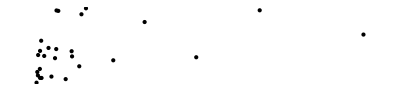

```mathematica
Graphics[
Table[Point[koordinate[d]],{d,drzave}]
]
```